```mathematica
Exit[]
```

```mathematica
b1=4.5;b2=1/(1-1/1.79);b3=8.4;
```

```mathematica
G1=(b1-1);G2=a(b2-1);G3=b(b3-1);
```

```mathematica
f=Max[0,Min[G1+G3-a,G2-1+G3,G2-1-b,G3-1-a]];
```

```mathematica
Plot3D[f,{a,0,10},{b,0,1}]
```

-Graphics3D-

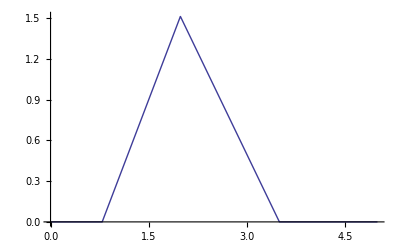

```mathematica
Plot[f/.b->0.0,{a,0,5}]
```